# a1 and a2

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->-t]
```

```mathematica
β[ω,δ,t,ϵ,7]
```

{{ⅈ δ-ϵ+ω,t,0,0,0,0,0},{t,ⅈ δ-ϵ+ω,t,0,0,0,0},{0,t,ⅈ δ-ϵ+ω,t,0,0,0},{0,0,t,ⅈ δ-ϵ+ω,t,0,0},{0,0,0,t,ⅈ δ-ϵ+ω,t,0},{0,0,0,0,t,ⅈ δ-ϵ+ω,t},{0,0,0,0,0,t,ⅈ δ-ϵ+ω}}

```mathematica
T1[t_,m_]:= t*IdentityMatrix[m]
```

```mathematica
Clear[T]
```

```mathematica
T[t_,m_]:=T[t,m]=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=t*IdentityMatrix[m];MAT]
```

```mathematica
Clear[leads]
```

```mathematica
leads[y_]:=leads[y]=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_"<>ToString[y]<>"_lead_"<>ToString[x]<>"_.dat"]],{x,Range[-3,3,0.01]}]
```

```mathematica
leads[10]
```

{1}
 |  |  |  |

```mathematica
Clear[leads]
```

```mathematica
leads=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/sq_lattice/50sq/leads/l"<>ToString[x]<>".dat"]],{x,Range[-2.5,2.5,0.01]}]
```

{1}
 |  |  |  |

```mathematica
Dimensions[leads]
```

{501,50,50}

```mathematica
LEFT[ω_,m_]:=LEFT[ω,m]=leads[m][[Round[ω*100+251]]]
```

```mathematica
f1[y_,start_,stop_]:= Table[{x,y},{x,start,stop}]
```

```mathematica
s[xstart_,xstop_,ystart_,ystop_]:=Module[{J=f1[ystart,xstart,xstop]},Do[J=Join[f1[y,xstart,xstop],J],{y,ystart+1,ystop}];J=J]
```

```mathematica
Clear[dist]
```

```mathematica
dist[total_,concentration_]:=dist[total,concentration]=Table[SortBy[Join[RandomSample[Join[s[1,50,1,25]],concentration],RandomSample[Join[s[1,50,26,50]],total-concentration]],First],1000]
```

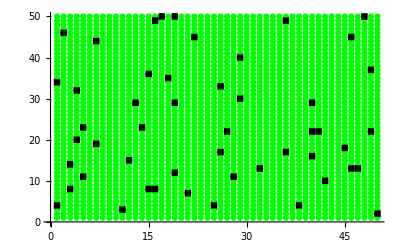

```mathematica
ListPlot[{Join[s[1,50,1,50]],dist[50,30][[1]]},PlotMarkers->Automatic,PlotStyle->{Green,Black}]
```

```mathematica
$Failed$Failed$Failed
```

```mathematica
TLD[start_]:=Module[{mat=RandomInteger[0,{50,50}]},ReplacePart[mat,Table[{a,a},{a,start,start+50-1}]->1]];SLLEAD[ω_,start_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[start;;start+50-1,start;;start+50-1]]=LEFT[ω,50];MAT];SRLEAD[ω_,start_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[start;;start+50-1,start;;start+50-1]]=LEFT[ω,50];
MAT]
```

```mathematica
f[ω_,δ_,t_,ϵ_,ϵ1_,unitcell_,total_,concentration_,number_]:=Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell,abc=dist[total,concentration][[number]]},If[abc[[loc1,1]]==m,ReplacePart[J,{{abc[[loc1,2]],abc[[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,total}];J]]
```

```mathematica
Clear[CA,TLD,SLLEAD,SRLEAD,recurs,ir,il,gdd1,grr1,Gnonlocalrl,GNON1,TRA]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ,50]]
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,leadleft_,leadright_,total_,concentration_,number_]:= Module[{sizeoflead=10,TLD,SRLEAD,SLLEAD},
TLD[start_]:=Module[{mat=RandomInteger[0,{50,50}]},ReplacePart[mat,Table[{a,a},{a,start,start+sizeoflead-1}]->t]];SLLEAD[start_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[start;;start+sizeoflead-1,start;;start+sizeoflead-1]]=LEFT[ω,sizeoflead];MAT];SRLEAD[start_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[start;;start+sizeoflead-1,start;;start+sizeoflead-1]]=LEFT[ω,sizeoflead];
MAT];
recurs=Module[{J1= SLLEAD[1]},
Do[
J1=Inverse[IdentityMatrix[50]-f[ω,δ,t,ϵ,ϵ1,unitcell,total,concentration,number].T1[1,50].J1.T1[1,50]].f[ω,δ,t,ϵ,ϵ1,unitcell,total,concentration,number],{unitcell,50}];J1=J1];ir=Inverse[IdentityMatrix[50]-SRLEAD[41].TLD[41].recurs.TLD[41]].SRLEAD[41];il=Inverse[IdentityMatrix[50]-recurs.TLD[41].SRLEAD[41].TLD[41]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.TLD[41].recurs;
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.TLD[41].grr1.TLD[41]-TLD[41].GNON1.TLD[41].GNON1]];TRA]
```

```mathematica
Table[{ω,Mean[ParallelTable[CA[ω,0.0001,1,0,1,1,41,100,50,n],{n,500}]]},{ω,Range[0,2.5,0.01]}]
```

{{0.,2.43953},{0.01,2.31337},{0.02,2.28654},{0.03,2.26114},{0.04,2.28707},{0.05,2.29102},{0.06,2.2733},{0.07,2.3002},{0.08,2.33645},{0.09,2.38062},{0.1,2.42595},{0.11,2.40233},{0.12,2.3967},{0.13,2.3315},{0.14,2.28158},{0.15,2.28873},{0.16,2.29391},{0.17,2.33972},{0.18,2.34767},{0.19,2.41136},{0.2,2.47929},{0.21,2.47602},{0.22,2.45182},{0.23,2.50914},{0.24,2.50567},{0.25,2.50024},{0.26,2.44468},{0.27,2.4491},{0.28,2.44289},{0.29,2.41866},{0.3,2.44463},{0.31,2.48462},{0.32,2.51242},{0.33,2.49049},{0.34,2.48246},{0.35,2.46262},{0.36,2.4804},{0.37,2.4588},{0.38,2.45169},{0.39,2.41731},{0.4,2.40485},{0.41,2.39595},{0.42,2.37885},{0.43,2.38965},{0.44,2.41203},{0.45,2.41288},{0.46,2.37194},{0.47,2.33469},{0.48,2.32437},{0.49,2.29293},{0.5,2.29901},{0.51,2.26728},{0.52,2.27478},{0.53,2.24363},{0.54,2.20031},{0.55,2.16605},{0.56,2.13509},{0.57,2.06898},{0.58,2.02594},{0.59,1.97686},{0.6,1.96243},{0.61,1.95101},{0.62,1.92541},{0.63,1.84713},{0.64,1.79563},{0.65,1.83139},{0.66,1.82073},{0.67,1.83851},{0.68,1.85352},{0.69,1.81462},{0.7,1.77355},{0.71,1.72404},{0.72,1.72256},{0.73,1.66088},{0.74,1.6559},{0.75,1.64461},{0.76,1.62521},{0.77,1.59058},{0.78,1.54956},{0.79,1.49957},{0.8,1.44256},{0.81,1.33838},{0.82,1.26113},{0.83,1.28785},{0.84,1.26376},{0.85,1.22975},{0.86,1.23137},{0.87,1.25808},{0.88,1.24357},{0.89,1.23024},{0.9,1.1715},{0.91,1.08717},{0.92,1.11144},{0.93,1.1363},{0.94,1.15136},{0.95,1.12237},{0.96,1.1271},{0.97,1.08562},{0.98,1.06287},{0.99,1.10852},{1.,1.06097},{1.01,0.95271},{1.02,0.935459},{1.03,0.973473},{1.04,0.979088},{1.05,0.973285},{1.06,0.971361},{1.07,0.956731},{1.08,0.968553},{1.09,0.897713},{1.1,0.88147},{1.11,0.859895},{1.12,0.817455},{1.13,0.788242},{1.14,0.791574},{1.15,0.831432},{1.16,0.799252},{1.17,0.76437},{1.18,0.786247},{1.19,0.827846},{1.2,0.959491},{1.21,0.896064},{1.22,0.81},{1.23,0.915828},{1.24,0.875606},{1.25,0.895879},{1.26,0.829728},{1.27,0.862458},{1.28,0.80061},{1.29,0.855387},{1.3,0.927553},{1.31,0.858217},{1.32,0.932828},{1.33,0.936791},{1.34,1.00346},{1.35,0.926436},{1.36,1.03219},{1.37,1.00075},{1.38,1.02794},{1.39,0.987914},{1.4,0.882418},{1.41,0.784535},{1.42,0.855032},{1.43,0.924146},{1.44,1.07163},{1.45,0.984106},{1.46,1.14028},{1.47,1.1249},{1.48,1.15566},{1.49,1.10847},{1.5,1.20747},{1.51,1.05792},{1.52,0.963966},{1.53,0.845185},{1.54,1.01559},{1.55,1.19475},{1.56,1.3553},{1.57,1.39296},{1.58,1.27672},{1.59,1.44154},{1.6,1.43987},{1.61,1.47581},{1.62,1.6715},{1.63,1.7203},{1.64,1.55448},{1.65,1.82178},{1.66,2.38435},{1.67,3.91598},{1.68,3.64537},{1.69,2.59039},{1.7,2.55404},{1.71,2.38376},{1.72,2.50429},{1.73,2.60633},{1.74,2.96172},{1.75,3.92724},{1.76,3.5634},{1.77,3.30264},{1.78,2.74919},{1.79,2.34528},{1.8,2.62545},{1.81,2.50034},{1.82,2.4272},{1.83,2.51095},{1.84,2.74916},{1.85,3.55206},{1.86,3.80713},{1.87,3.90014},{1.88,3.13507},{1.89,2.56989},{1.9,2.21999},{1.91,2.65245},{1.92,2.61656},{1.93,2.97475},{1.94,3.27918},{1.95,3.33416},{1.96,4.22552},{1.97,3.68608},{1.98,3.926},{1.99,3.43243},{2.,2.73976},{2.01,2.26689},{2.02,2.68651},{2.03,2.61537},{2.04,3.36827},{2.05,3.6301},{2.06,3.95799},{2.07,4.15996},{2.08,4.0845},{2.09,3.53869},{2.1,3.68862},{2.11,3.48857},{2.12,4.36567},{2.13,3.67275},{2.14,4.46481},{2.15,4.65181},{2.16,5.2039},{2.17,6.96979},{2.18,7.50573},{2.19,8.08447},{2.2,7.65523},{2.21,10.9734},{2.22,31.3462},{2.23,25.7205},{2.24,24.3236},{2.25,16.0648},{2.26,16.9584},{2.27,13.3507},{2.28,12.136},{2.29,9.40081},{2.3,8.27684},{2.31,10.4005},{2.32,5.96783},{2.33,7.09129},{2.34,7.50475},{2.35,8.2599},{2.36,7.08233},{2.37,5.13344},{2.38,6.60031},{2.39,6.20541},{2.4,3.93082},{2.41,4.47442},{2.42,4.82111},{2.43,3.33868},{2.44,3.81262},{2.45,3.96703},{2.46,4.45058},{2.47,5.07596},{2.48,3.50686},{2.49,3.47836},{2.5,2.91791}}

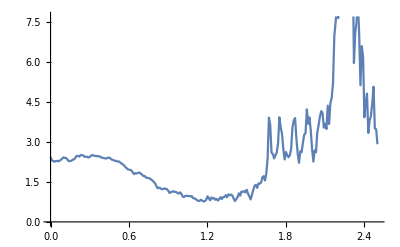

```mathematica
ListPlot[%15,Joined->True]
```

```mathematica
ListPlot[%15,Joined->True]
```

-Graphics-

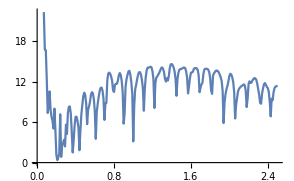

```mathematica
ListPlot[Table[{ω,CA[ω,0.0001,1,0,1,100,50,1](*-Im[CA[ω,0.0001,1,0,0,100,40,1][[1,1]]]*)},{ω,Range[0,2.5,0.01]}],Joined->True]
```